```mathematica
<<emittanceEllipse`
```

```mathematica
<<sddsBinaryInterpret`
```

```mathematica
emitans=.
```

```mathematica
sddsBinaryInterpret["C:\\GPT\\Delta\\Johnny\\1pc_precut_original.sdds",sddsVerbose->True];
P={x,xp};
P=P[[All,Ordering[x][[1;;-1;;50]]]];
```

Number of Pages: 1

Variables (Re)Assigned: {x, y, t, xp, yp, p, q}

Parameters (Re)Assigned: {}

```mathematica
Dimensions[P]
```

{2,1000}

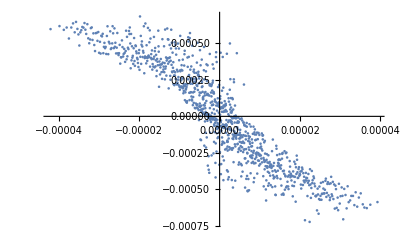

```mathematica
ListPlot[Transpose[P]]
```

sddsBinaryInterpret["c:\\mad\\clara\\v10\\test.0337.sdds"];
P = {x, xp};

```mathematica
emitans=emittanceEllipse[emitans,P,10^-6,0.68]
```

{{1.32513×10^-8,0.679},{6.60857×10^-6,0.000638265,0.0436858},{-4.21342,0.194538,96.3973}}

```mathematica
twissparams={√Det[Covariance[Transpose[P]]],#[[1,1]],#[[2,2]]}&[Covariance[Transpose[P]]/((√Det[Covariance[Transpose[P]]])/π)];
```

```mathematica
ellipseparams=Re[{a->(√(-(β-γ) (-β-γ+√(-4 π^2+(β+γ)^2)) ϵ))/(√2 π √(β-γ)),b->(√2 √(β-γ) ϵ)/(√(-(β-γ) (-β-γ+√(-4 π^2+(β+γ)^2)) ϵ)),c->ArcCos[-(√(-(4 π^2-(β+γ)^2-β √(-4 π^2+(β+γ)^2)+γ √(-4 π^2+(β+γ)^2))/((-2 π+β+γ) (2 π+β+γ))))/(√2)]}[[All,2]]/.{ϵ->π twissparams[[1]],β->twissparams[[2]],γ->twissparams[[3]]}];
```

```mathematica
10^6 √Det[Covariance[Transpose[P]]]
```

0.00209787

```mathematica
covellipse=Block[{a,b,c},
{a,b,c}=#;
Graphics[{Opacity[0.5],Red,Translate[Rotate[Scale[Disk[{0, 0}], Abs@{b,a}],c], {0, 0}]}]
]&[ellipseparams];
```

```mathematica
Show[emittanceEllipsePlot[P,emitans],covellipse]
```

-Graphics-

## Gaussian Beam

```mathematica
<<emittanceEllipse`
```

```mathematica
beam=generateGaussianBeamDistribution[10000,{5.6 10^-6,10^-6,0,0},{-5,10,-1,10},{0,0,0,0},{0,0,0,0}];
```

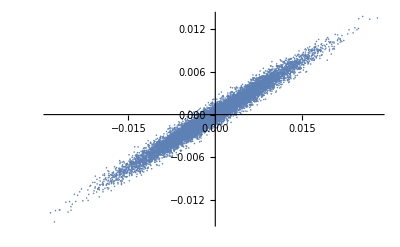

```mathematica
mathematicgaussbeam=ListPlot[beam⟦All,{1,2}⟧]
```

```mathematica
emitans=.;
```

```mathematica
P=Transpose[beam][[{1,2}]];
```

```mathematica
twissparams={√Det[Covariance[Transpose[P]]],#[[1,1]],-#[[1,2]],#[[2,2]]}&[Covariance[Transpose[P]]/(√Det[Covariance[Transpose[P]]])];
```

```mathematica
ellipseparams=Re[{a->√(ϵ β),b->√(ϵ/β),c->1/2 ArcTan[(2 α)/(γ-β)]}[[All,2]]/.{α->twissparams[[3]],β->twissparams[[2]],γ->twissparams[[4]],ϵ-> twissparams[[1]]}];
```

```mathematica
emitans={{0.,0.},ellipseparams,{0.,0.,0.}};
```

```mathematica
emitans=emittanceEllipse[emitans,P,10^-7,1-Exp[-0.5]]
```

{{5.4489×10^-6,0.3934},{0.00806691,0.000675463,0.453218},{4.66839,9.66914,2.35738}}

```mathematica
covellipse=Block[{a,b,c},
{a,b,c}=#;
Graphics[{Opacity[0.5],Red,Translate[Rotate[Disk[{0, 0}, Abs[{a, b}]], c], {0, 0}]},Frame->True]
]&[ellipseparams];
```

```mathematica
Show[emittanceEllipsePlot[P,emitans],covellipse,Frame->True,ImageSize->Large]
```

-Graphics-

## ASTRA Beam

```mathematica
<<emittanceEllipse`
```

```mathematica
<<sddsBinaryInterpret`
```

```mathematica
sddsBinaryInterpret["C:\\GPT\\Delta\\Johnny\\1pc_precut_original.sdds",sddsVerbose->True];
P={x,xp};
P=P[[All,Ordering[x][[1;;-1;;5]]]];
beam=Transpose[P];
```

Number of Pages: 1

Variables (Re)Assigned: {x, y, t, xp, yp, p, q}

Parameters (Re)Assigned: {}

```mathematica
beam=generateGaussianBeamDistribution[10000,{5.6 10^-6,10^-6,0,0},{-2,10,-1,10},{0,0,0,0},{0,0,0,0}];
```

```mathematica
γ=0.511Mean[p]
```

51.4508

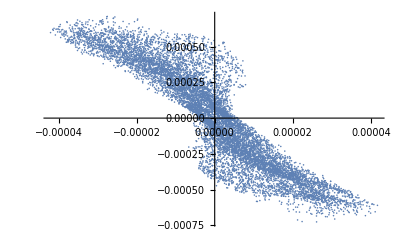

```mathematica
mathematicgaussbeam=ListPlot[beam⟦All,{1,2}⟧]
```

```mathematica
emitans=.;
```

```mathematica
P=Transpose[beam][[{1,2}]];
```

```mathematica
emitans=emitansg=emittanceGaussian[P]
```

{{2.20696×10^-9,0.393469},{0.000346819,6.36343×10^-6,1.61057},{2.16476,0.104495,54.4158}}

```mathematica
emitans=emittanceEllipse[emitans,P,10^-5,N[1-Exp[-1^2/2]]]
```

{{1.75683×10^-9,0.3928},{0.000401058,4.38047×10^-6,1.6062},{3.23867,0.125643,91.4412}}

```mathematica
covellipse=Block[{a,b,c},
{a,b,c}=#[[2]];
Graphics[{Opacity[0.3],Red,Translate[Rotate[Scale[Disk[{0, 0}, Abs[{a,b}]],1], c], {0, 0}]},Frame->True]
]&[emitansg];
Show[emittanceEllipsePlot[P,emitans],covellipse,Frame->True,ImageSize->Large]
```

-Graphics-

```mathematica
10^6 γ emitansg[[1,1]]
```

0.11355

```mathematica
10^6 γ emitans[[1,1]]
```

0.09039

```mathematica
100(twissparams[[1]]/emitans[[1,1]]-1)
```

25.6219